# Bloch-Messiah Decompositions

The entire optical circuit that generates GPS breeding w/ post selection output states (the GPS state generation, breeding, and damping operation) can be simplified to an optical circuit with squeezed vacuum inputs operated on with passive Gaussian optics using Bloch-Messiah decomposition. Here we perform the Bloch-Messiah decomposition to find the input squeezing values and passive Gaussian circuit parameters needed to produce each of the final output states.

## Functions

```mathematica
TwoModeOutProb[n_,σ_] :=Module[{P, σ12, σ22, σdet},
σdet = Det[σ];
σ12 = σ[[1,2]];
σ22 = σ[[2,2]];
P = (Factorial[2*n]/(8^n Factorial[n]^2))Sqrt[σdet]*σ12^(2*n)*((1/2)(σdet+σ22))^(-n-1/2);
Return[P];
];
TwoModeOutWF[n_,σ_]:=Module[{ψ, σ12, σ22, σdet},
σdet = Det[σ];
σ12 = σ[[1,2]];
σ22 = σ[[2,2]];
ψ = (1/Pi)^(1/4)*(-2)^n*Sqrt[Factorial[n]/Factorial[2*n]]*((1/2)(σdet + σ22))^((2*n+1)/4)*x^n Exp[(1/4)(-(σdet+σ22))x^2];
Return[ψ];
];
SqVacCoVar[rVec_]:= (1/2)*DiagonalMatrix[Exp[2*Flatten[{rVec,-1*rVec}]]];
DisplacedSqueezedMoments[alphaVec_, xiVec_]:=Module[{d,V, r, phi},
r = Sqrt[Re[xiVec]^2+Im[xiVec]^2];
phi =Arg[xiVec];
d = Flatten[Sqrt[2]*{Re[alphaVec],Im[alphaVec]}];
V = (1/2)*ArrayFlatten[{{DiagonalMatrix[Cosh[2r]+Sinh[2r]*Cos[phi]], -DiagonalMatrix[Sinh[2*r]*Sin[phi]]},{-DiagonalMatrix[Sinh[2*r]*Sin[phi]],DiagonalMatrix[Cosh[2r]-Sinh[2r]*Cos[phi]]}}];
Return[{d,V}];
];
BSTransform[N_,n_,m_,tau_]:=Module[{S,s,M},
M = {{Sqrt[tau]},{-Sqrt[tau],Sqrt[1-tau]}};
s = IdentityMatrix[N];
s[[n,n]] = Sqrt[1-tau];
s[[n,m]] = Sqrt[tau];
s[[m,n]]=-Sqrt[tau];
s[[m,m]]=Sqrt[1-tau];
S = ArrayPad[s,{{0,N},{0,N}}]+ArrayPad[s,{{N,0},{N,0}}];
Return[S];
];
OmegaCreate[Modes_]:= ArrayFlatten[TensorProduct[{{0,1},{-1,0}},IdentityMatrix[Modes]]];
PolarDecomposition[mat_]/;MatrixQ[mat,NumericQ]:=
Module[{n=Last[Dimensions[mat]],prec=Internal`EffectivePrecision[mat],cv,u,s,v},
({u,s,v}=SingularValueDecomposition[N[mat,prec],Tolerance->0];
cv=ConjugateTranspose[v];
{Take[u,All,n].cv,v.Take[s,n].cv})/;prec<∞]
TCreate[N_,n_,m_] := Module[{T},
T = IdentityMatrix[N];
T[[n,n]] = Exp[I*phi]*Cos[theta];
T[[n,m]] = -Sin[theta];
T[[m,n]] = Exp[I*phi]*Sin[theta];
T[[m,m]] = Cos[theta];
Return[T];
];
UnitaryDecomp[U_]:=Module[{phi,theta,r},
r =U[[2,1]]/U[[2,2]];
theta = ArcTan[Abs[r]];
phi =Arg[r];
Return[{phi,theta}];
];
Enumerate[x_]:=Module[{xCon,Output},
xCon = Range[1,Length[x],1];
Output = Table[{x[[ii]],xCon[[ii]]},{ii,1,Length[x]}];
Return[Output];
];
nullTi[ii_,jj_,Eles_,U_]:=Module[{theta,phi,nmax,r,n,m, CurrentEle},
n=ii-jj;
m=ii-jj+1;
nmax = Dimensions[U][[1]];
theta = {};
CurrentEle=Eles[[ii,jj+1]];
If[Chop[U[[CurrentEle[[1]],CurrentEle[[2]]]]]==0,
theta = 0;
phi = 0;
];
If[Chop[U[[CurrentEle[[1]],CurrentEle[[2]]+1]]]==0,
theta = Pi/2;
phi = 0;
];
If[Length[theta]==0,
r =U[[CurrentEle[[1]],CurrentEle[[2]]]]/U[[CurrentEle[[1]],CurrentEle[[2]]+1]];
theta = ArcTan[Abs[r]];
phi =Arg[r];
];
Return[{n,m,phi,theta,nmax}];
];
nullT[ii_,jj_,Eles_,U_]:=Module[{theta,phi,nmax,r,n,m,CurrentEle},
nmax = Dimensions[U][[1]];
n=nmax+jj-ii-1;
m=nmax+jj-ii;
theta = {};
CurrentEle=Eles[[ii,jj]];
If[Chop[U[[CurrentEle[[1]],CurrentEle[[2]]]]]==0,
theta = 0;
phi = 0;
];
If[Chop[U[[CurrentEle[[1]]-1,CurrentEle[[2]]]]]==0,
theta = Pi/2;
phi = 0;
];
If[Length[theta]==0,
r =U[[CurrentEle[[1]],CurrentEle[[2]]]]/U[[CurrentEle[[1]]-1,CurrentEle[[2]]]];
theta = ArcTan[Abs[r]];
phi =Arg[r];];
Return[{n,m,phi,theta,nmax}];
];
T[n_,m_, phi_,theta_, nmax_]:=Module[{mat},
mat=IdentityMatrix[nmax];
mat[[m,m]]=Exp[I*phi]*Cos[theta];
mat[[m,n]]=-Sin[theta];
mat[[n,m]]=Exp[I*phi]*Sin[theta];
mat[[n,n]]=Cos[theta];
Return[mat];
];
Ti[n_,m_, phi_,theta_, nmax_]:=Module[{mat},
mat=Inverse[T[n,m, phi,theta, nmax]];
Return[mat];
];
Rectangular[U_]:= Module[{tilist,tlist,localU,nsize,Eles,TempH},
localU = U;
nsize = Dimensions[U][[1]];
Eles = If[Mod[nsize,2]!=0,Table[If[Mod[kk,2]!=0,Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk],Reverse[Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk]]],{kk,nsize-1,1,-1}],Table[If[Mod[kk,2]==0,Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk],Reverse[Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk]]],{kk,nsize-1,1,-1}]];
tilist = {};
tlist = {};
For[ii=1, ii<=nsize-1,ii++,
If[Mod[ii,2]!= 0,
For[jj=0,jj<=ii-1,jj++,If[ii==3&&jj==1,
TempH = nullTi[ii,jj,Eles,localU];
TempH[[3]]=0;
AppendTo[tilist,TempH];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];
,AppendTo[tilist,nullTi[ii,jj,Eles,localU]];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];];
(*AppendTo[tilist,nullTi[ii,jj,Eles,localU]];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];*)
],
For[jj=1,jj<=ii,jj++,
AppendTo[tlist,nullT[ii,jj,Eles,localU]];
localU = T[tlist[[-1]][[1]],tlist[[-1]][[2]],tlist[[-1]][[3]],tlist[[-1]][[4]],tlist[[-1]][[5]]].localU;
];
];
];
Return[{Reverse[tilist],Reverse[tlist],localU}];
];
Rectangular3[U_]:= Module[{tilist,tlist,localU,nsize,Eles,TempH},
localU = U;
nsize = Dimensions[U][[1]];
Eles = If[Mod[nsize,2]!=0,Table[If[Mod[kk,2]!=0,Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk],Reverse[Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk]]],{kk,nsize-1,1,-1}],Table[If[Mod[kk,2]==0,Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk],Reverse[Diagonal[Table[If[LowerTriangularize[ArrayReshape[Range[1,nsize^2,1],{nsize,nsize}],-1][[ii,jj]]!= 0,{ii,jj}],{ii,1,nsize},{jj,1,nsize}],-kk]]],{kk,nsize-1,1,-1}]];
tilist = {};
tlist = {};
For[ii=1, ii<=nsize-1,ii++,
If[Mod[ii,2]!= 0,
For[jj=0,jj<=ii-1,jj++,If[ii==3&&jj==1,
TempH = nullTi[ii,jj,Eles,localU];
AppendTo[tilist,TempH];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];
,AppendTo[tilist,nullTi[ii,jj,Eles,localU]];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];];
(*AppendTo[tilist,nullTi[ii,jj,Eles,localU]];
localU = localU.Ti[tilist[[-1]][[1]],tilist[[-1]][[2]],tilist[[-1]][[3]],tilist[[-1]][[4]],tilist[[-1]][[5]]];*)
],
For[jj=1,jj<=ii,jj++,
AppendTo[tlist,nullT[ii,jj,Eles,localU]];
localU = T[tlist[[-1]][[1]],tlist[[-1]][[2]],tlist[[-1]][[3]],tlist[[-1]][[4]],tlist[[-1]][[5]]].localU;
];
];
];
Return[{Reverse[tilist],Reverse[tlist],localU}];
];
RectangularPhaseEnd[U_]:= Module[{DD,tilist,tlist,diags,newtlist,newdiags,em,en,newtheta, newphi,theta,phi,alpha,beta,CurrentT,newCurrentT,nsize,newalpha,newbeta},
{tilist,tlist,DD} = Rectangular[U];
diags = Diagonal[DD];
nsize = Length[diags];
newtlist = tilist;
newdiags = diags;
tlist = tlist;
For[ii=1,ii<=Length[tlist],ii++,
CurrentT = tlist[[ii]];
em= CurrentT[[1]];
en= CurrentT[[2]];
alpha = Arg[newdiags[[em]]];
beta = Arg[newdiags[[en]]];
phi = CurrentT[[3]];
theta = CurrentT[[4]];
newtheta=theta;
newphi=beta-alpha+Pi;
newalpha=alpha;
newbeta=alpha-phi+Pi;
newCurrentT = {CurrentT[[1]],CurrentT[[2]],newphi,newtheta,nsize};
PrependTo[newtlist,newCurrentT];
newdiags[[em]] = Exp[I*newalpha];
newdiags[[en]] = Exp[I*newbeta];
];
Return[{newtlist,newdiags}];
];
Rectangular3PhaseEnd[U_]:= Module[{DD,tilist,tlist,diags,newtlist,newdiags,em,en,newtheta, newphi,theta,phi,alpha,beta,CurrentT,newCurrentT,nsize,newalpha,newbeta},
{tilist,tlist,DD} = Rectangular3[U];
diags = Diagonal[DD];
nsize = Length[diags];
newtlist = tilist;
newdiags = diags;
tlist = tlist;
For[ii=1,ii<=Length[tlist],ii++,
CurrentT = tlist[[ii]];
em= CurrentT[[1]];
en= CurrentT[[2]];
alpha = Arg[newdiags[[em]]];
beta = Arg[newdiags[[en]]];
phi = CurrentT[[3]];
theta = CurrentT[[4]];
newtheta=theta;
newphi=beta-alpha+Pi;
newalpha=alpha;
newbeta=alpha-phi+Pi;
newCurrentT = {CurrentT[[1]],CurrentT[[2]],newphi,newtheta,nsize};
PrependTo[newtlist,newCurrentT];
newdiags[[em]] = Exp[I*newalpha];
newdiags[[en]] = Exp[I*newbeta];
];
Return[{newtlist,newdiags}];
];
```

## Solving for relevant parameters

```mathematica
nSpace = DeleteCases[DeleteCases[Range[7,40],37],39];
```

For each n, the squeezing (dB) that each GPS output state should have in order for breeding to result in proper GKP spacing is given in the following analytical form. Note that n > 7 for r ∈ Reals

```mathematica
OptCatStateSqueezingdB = Table[{nSpace[[ii]],10*Log10[Exp[ArcCosh[nSpace[[ii]]/(2*Pi)]]]},{ii,1,Length[nSpace]}];
```

The squeezing (dB) that gives maximum probability for each number of photons detected (n) in the GPS set up is

```mathematica
MaxGPSProbSqueezingdB = Table[10*Log10[Exp[ArcSech[1/(1+2*nSpace[[ii]])]]],{ii,1,Length[nSpace]}];
```

If the state after PNR has squeezing r1 and we unsqueeze by r2,  r2 must follow the equation below for the unsqueezed state to be a GPS state with some target squeezing r,

```mathematica
PostSqueezingdBCond =r2dB/.FullSimplify[Solve[ⅇ^(-2 Log[10^(r2dB/10)]/2) Cosh[2 r1]==Cosh[2 r],r2dB,Assumptions->{r2dB ∈ Reals, r1>0,r>0}][[1]],Assumptions->{r1>r}]
```

(10 Log[Cosh[2 r1] Sech[2 r]])/Log[10]

To have maximum GPS successes probability and correct GKP spacing, the post PNR squeezing is found by subbing in the max prob squeezing and squeezing that gives optimal spacing for breeding into the condition found above

```mathematica
OptSpacingPostSqueezing =Table[PostSqueezingdBCond/.{r1->Log[10^(MaxGPSProbSqueezingdB[[ii]]/10)]/2,r->Log[10^(OptCatStateSqueezingdB[[ii,2]]/10)]/2},{ii,1,Length[nSpace]}];
```

## GPS w/ squeezing auxiliary operation symplectic diagonalization and Bloch-Messiah decompositions

First, we analytically decompose the GPS circuit with the  squeezing auxiliary operation such that the post GPS squeezing is moved to the beginning of the circuit. We will perform the symplectic diagonalization and Bloch-Messiah Decomposition of the Wigner function covariance matrix

Set number of modes

```mathematica
Modes =2;
```

Generate GPS input covariance matrix

```mathematica
{d, V0} = FullSimplify[DisplacedSqueezedMoments[ConstantArray[0,2*Modes], {-r1,r1}],Assumptions->{r1 > 0}];
```

Create and apply GPS beam splitter transformation

```mathematica
S =BSTransform[Modes,1,2, R];
V = FullSimplify[S.V0.Transpose[S],Assumptions->{r1 ∈ Reals, 0<φ1<2*Pi, r2 ∈ Reals,  0<φ2<2*Pi, 0<R<1}];
```

Find GPS beam splitter condition

```mathematica
Con= FullSimplify[Solve[ⅇ^(2 r1)-2 R Sinh[2 r1]==1,R][[1]],Assumptions->r1>0];
```

Apply GPS condition

```mathematica
V = FullSimplify[V/.Con,Assumptions->r1>0];
```

Apply squeezing auxiliary operation

```mathematica
V = FullSimplify[{{1,0,0,0},{0,Exp[r2],0,0},{0,0,1,0},{0,0,0,Exp[-r2]}}.V.{{1,0,0,0},{0,Exp[r2],0,0},{0,0,1,0},{0,0,0,Exp[-r2]}},Assumptions->{r1>0,r2>0}];
```

Performing symplectic diagonalization

```mathematica
Ω = OmegaCreate[Modes];
Db = DiagonalMatrix[ConstantArray[1/2,2*Modes]];
```

```mathematica
VInv =FullSimplify[4*(Ω.V.Transpose[Ω]),Assumptions->{r1>0,r2>0}];
(*FullSimplify[VInv-Inverse[V],Assumptions->{r1>0,r2>0}]== ConstantArray[0,{4,4}]*)
```

```mathematica
Mm12 = FullSimplify[Assuming[{r1>0,r2>0},MatrixPower[VInv,1/2]],Assumptions->{r1>0,r2>0}];
SPrime =FullSimplify[Ω.Transpose[Mm12.MatrixPower[Db,1/2]].Transpose[Ω],Assumptions->{r1>0,r2>0}];
SymplecticQ =FullSimplify[SPrime.Ω.Transpose[SPrime],Assumptions->{r1>0,r2>0}] ==Ω (*Check that SPrime is a symplectic matrix*)
FullSimplify[FullSimplify[SPrime.Db.Transpose[SPrime],Assumptions->{ r1>0,r2>0}]-V,Assumptions->{r1>0,r2>0}]== ConstantArray[0,{4,4}] (*Check that application of SPrime to vacuum covariance matrix recovers the origonal final covariance matrix, V*)
```

Getting the symplectic transformation to perform on vacuum for every n with appropriate r1 and r2 for max fidelity and probability

```mathematica
Get["Bloch Messiah Decompositions/SPrime"];
```

```mathematica
OptSPrimeTable = N[Table[SPrime /.{r1->Log[10^(MaxGPSProbSqueezingdB[[ii]]/10)]/2,r2->Log[10^(OptSpacingPostSqueezing[[ii]]/10)]/2},{ii,1,Length[nSpace]}]];
```

Performing Bloch-Messiah Decomposition numerically

```mathematica
SVDTable = Table[SingularValueDecomposition[OptSPrimeTable[[ii]]],{ii,1,Length[nSpace]}];
SqueezingTransformationTable = SVDTable[[;;,2]];
PassiveTransformationTable = SVDTable[[;;,1]];
PassiveUnitaryTable = Table[PassiveTransformationTable[[ii,1;;2,1;;2]]+I*PassiveTransformationTable[[ii,3;;4,1;;2]],{ii,1,Length[nSpace]}];
UnitaryTest = Total[Boole[Table[UnitaryMatrixQ[PassiveUnitaryTable[[ii]]],{ii,1, Length[nSpace]}]]]==Length[nSpace](*Check that decompostion resulted in unitary matrices*)
```

True

Extracting squeezing, transmissivities, and phases from unitary matrices

```mathematica
SqueezingValuesTable = Table[{y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,1,1]],x][[1]],y]][[1]],y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,2,2]],x][[1]],y]][[1]]},{ii,1,Length[nSpace]}];
BSandPSTable = Table[UnitaryDecomp[PassiveUnitaryTable[[ii]]],{ii,1,Length[nSpace]}];
```

With the new input squeezing values, beam, splitters, and phase shifters we check that we get the correct covariance matrix

```mathematica
W = 1/Sqrt[2] ArrayFlatten[{{IdentityMatrix[2],IdentityMatrix[2]},{-I*IdentityMatrix[2],I*IdentityMatrix[2]}}];
DecompCheckUnitaryTable = Table[IdentityMatrix[2].TCreate[2,1,2]/.{phi->BSandPSTable[[ii,1]],theta->BSandPSTable[[ii,2]]} ,{ii,1,Length[nSpace]}]//Chop;(*Assemble passive unitary from beam splitter and phase values*)
DecompCheckPassiveSymplecticTable = Table[W.ArrayFlatten[{{DecompCheckUnitaryTable[[ii]],ConstantArray[0,{2,2}]},{ConstantArray[0,{2,2}],Conjugate[DecompCheckUnitaryTable[[ii]]]}}].Transpose[Conjugate[W]],{ii,1,Length[nSpace]}];(*Convert passive unitary to symplectic transformation to apply to covariance matrix*)
DecompCheckActiveSymplecticTable = Table[DiagonalMatrix[{Exp[-(Log[10^(SqueezingValuesTable[[ii,1]]/10)]/2)],Exp[-(Log[10^(SqueezingValuesTable[[ii,2]]/10)]/2)],Exp[(Log[10^(SqueezingValuesTable[[ii,1]]/10)]/2)],Exp[(Log[10^(SqueezingValuesTable[[ii,2]]/10)]/2)]}],{ii,1,Length[nSpace]}];(*Assemble active squeezing symplectic tranformation *)
DecompCheckTotalSymplecticTable = Table[DecompCheckPassiveSymplecticTable[[ii]].DecompCheckActiveSymplecticTable[[ii]],{ii,1,Length[nSpace]}];(*Assemble total symplectic tranformation, squeezing then passive transformation *)
DecompCheckCovarianceMatrixTable = Table[DecompCheckTotalSymplecticTable[[ii]].Db.Transpose[DecompCheckTotalSymplecticTable[[ii]]],{ii,1,Length[nSpace]}]//Chop;(*Apply total symplectic tranformation to vacuum*)
DecompCheckVTable = Table[V/.{r1->Log[10^(MaxGPSProbSqueezingdB[[ii]]/10)]/2,r2->Log[10^(OptSpacingPostSqueezing[[ii]]/10)]/2},{ii,1,Length[nSpace]}]//Chop;(*Substitute numerical values into origonal final covaraince matrix to compare to*)
DecompCheck = Total[Boole[Table[Chop[DecompCheckVTable[[ii]]-DecompCheckCovarianceMatrixTable[[ii]]]==ConstantArray[0.,{4,4}],{ii,1,Length[nSpace]}]]]==Length[nSpace]
```

True

## GPS breeding w/ damping auxiliary operation damping symplectic diagonalization and Bloch-Messiah decompositions

Now that we have decomposed the GPS circuit w/ squeezing auxiliary operation, so that is it is squeezed vacuum states followed by beam splitters and PNR detection, we can now apply the Gaussian circuit that does the breeding step and damping (when applicable).  We then perform symplectic diagonalization and Bloch-Messiah decomposition such that  the inline squeezing that occurs in the QND interaction of the damping operation is moved to the beginning of the circuit.

To begin, we get two copies of the decomposed GPS circuit w/ squeezing auxiliary operation covariance matrices and compose them to make a 4 mode covariance matrix +1 more mode for damping operation.

Set number of modes

```mathematica
Modes =5;
```

Retrieve the subset of nSpace where damping provides fidelity improvement and the optimal squeezing to use for damping (DampingSqdBTable) in each case

```mathematica
Get["Figure 2/DampingSqdBTable"];
Get["Bloch Messiah Decompositions/nSpaceFilteredForDampingImprovment"];
```

Permutation to change qpqp to qqpp

```mathematica
Π = Normal[PermutationMatrix[{1,5,2,6,9,3,7,4,8,10}]];
V0Table =Table[If[nSpace[[ii]]>Last[nSpaceFilteredForDampingImprovment],Π.Normal[BlockDiagonalMatrix[{DecompCheckVTable[[ii]],DecompCheckVTable[[ii]],DisplacedSqueezedMoments[ConstantArray[0,1*2], {0.}][[2]]}]].Transpose[Π],Π.Normal[BlockDiagonalMatrix[{DecompCheckVTable[[ii]],DecompCheckVTable[[ii]],DisplacedSqueezedMoments[ConstantArray[0,1*2], {Log[10^(DampingSqdBTable[[ii,2]]/10)]/2}][[2]]}]].Transpose[Π]],{ii,1,Length[nSpace]}];
```

Create and apply balanced beam splitter transformation for breeding

```mathematica
S =BSTransform[5,3,4,1/2];
VTable = Table[S.V0Table[[ii]].Transpose[S],{ii,1,Length[nSpace]}];
```

Create and apply QND interaction for damping operation

```mathematica
S1 =BSTransform[2,1,2,1-(5+Sqrt[5])/10];
S2 = DiagonalMatrix[{Exp[ArcSinh[1/2]],Exp[-ArcSinh[1/2]],Exp[-ArcSinh[1/2]],Exp[ArcSinh[1/2]]}];
S3 =BSTransform[2,2,1,(5+Sqrt[5])/10];
SQND = Normal[PermutationMatrix[{1,2,3,7,8,4,5,6,9,10}]].BlockDiagonalMatrix[{IdentityMatrix[6],FullSimplify[S3.S2.S1]}].Transpose[Normal[PermutationMatrix[{1,2,3,7,8,4,5,6,9,10}]]];
VPrimeTable = Table[If[nSpace[[ii]]>Last[nSpaceFilteredForDampingImprovment],VTable[[ii]],SQND.VTable[[ii]].Transpose[SQND]],{ii,1,Length[nSpace]}];
```

Performing symplectic diagonalization

```mathematica
Ω = OmegaCreate[Modes];
Db = DiagonalMatrix[ConstantArray[1/2,2*Modes]];
```

```mathematica
VPrimeInvTable =Table[FullSimplify[4*(Ω.VPrimeTable[[ii]].Transpose[Ω])],{ii,1,Length[nSpace]}];
(*Total[Boole[Table[Chop[VPrimeInvTable[[ii]]-Inverse[VPrimeTable[[ii]]]]== ConstantArray[0.,{10,10}],{ii,1,Length[nSpaceFilteredDampingImprovment]}]]] == Length[nSpaceFilteredDampingImprovment]*)
```

```mathematica
Mm12Table = Table[MatrixPower[VPrimeInvTable[[ii]],1/2],{ii,1,Length[nSpace]}];
SPrimeTable =Table[Ω.Transpose[Mm12Table[[ii]].MatrixPower[Db,1/2]].Transpose[Ω],{ii,1,Length[nSpace]}];
SymplecticQ =Total[Boole[Table[Chop[SPrimeTable[[ii]].Ω.Transpose[SPrimeTable[[ii]]]- Ω]== ConstantArray[0.,{10,10}],{ii,1,Length[nSpace]}]]] ==Length[nSpace](*Check that SPrimes are symplectic matricies*)
Total[Boole[Table[Chop[SPrimeTable[[ii]].Db.Transpose[SPrimeTable[[ii]]]-VPrimeTable[[ii]]]==ConstantArray[0.,{10,10}],{ii,1,Length[nSpace]}]]]==Length[nSpace] (*Check that application of SPrimes to vacuum covariance matricies recovers the origonal final covariance matricies, VPrimeTable*)
```

True

True

Performing Bloch-Messiah Decomposition

```mathematica
SVDTable = Table[SingularValueDecomposition[SPrimeTable[[ii]]],{ii,1,Length[nSpace]}];
SqueezingTransformationTable = SVDTable[[;;,2]];
PassiveTransformationTable = SVDTable[[;;,1]];
PassiveUnitaryTable = Table[PassiveTransformationTable[[ii,1;;5,1;;5]]+I*PassiveTransformationTable[[ii,6;;10,1;;5]],{ii,1,Length[nSpace]}];
UnitaryTest = Total[Boole[Table[UnitaryMatrixQ[PassiveUnitaryTable[[ii]]],{ii,1, Length[nSpace]}]]]==Length[nSpace](*Check that decompostion resulted in unitary matrices*)
```

True

Extracting squeezing, transmissivities, and phases from unitary matrices

```mathematica
nPhaseFlip = nSpace[[{5,22,24,27,28,29,30,32}]];
PostDampingSqueezingValuesTable = Table[{y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,1,1]],x][[1]],y]][[1]],y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,2,2]],x][[1]],y]][[1]],y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,3,3]],x][[1]],y]][[1]],y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,4,4]],x][[1]],y]][[1]],y/.Quiet[Solve[Log[10^(y/10)]/2 ==x/.NSolve[Exp[x]==SqueezingTransformationTable[[ii,5,5]],x][[1]],y]][[1]]},{ii,1,Length[nSpace]}];
PostDampingBSandPSTable = Table[If[MemberQ[nPhaseFlip,nSpace[[ii]]],Rectangular3PhaseEnd[PassiveUnitaryTable[[ii]]],RectangularPhaseEnd[PassiveUnitaryTable[[ii]]]],{ii,1,Length[nSpace]}];
```

With the new squeezing values, beam, splitters, and phase shifters we check that we get the correct covariance matrix

```mathematica
W = 1/Sqrt[2] ArrayFlatten[{{IdentityMatrix[Modes],IdentityMatrix[Modes]},{-I*IdentityMatrix[Modes],I*IdentityMatrix[Modes]}}];
DecompCheckUnitaryTable ={};
For[ii=1,ii<=Length[nSpace],ii++, 
CombinedUnitaryTable = IdentityMatrix[Modes];
For[kk=1,kk<=Length[PostDampingBSandPSTable[[ii,1]]],kk++,
CombinedUnitaryTable = CombinedUnitaryTable.T[PostDampingBSandPSTable[[ii,1]][[kk,1]],PostDampingBSandPSTable[[ii,1]][[kk,2]],PostDampingBSandPSTable[[ii,1]][[kk,3]],PostDampingBSandPSTable[[ii,1]][[kk,4]],PostDampingBSandPSTable[[ii,1]][[kk,5]]];
];
AppendTo[DecompCheckUnitaryTable,DiagonalMatrix[PostDampingBSandPSTable[[ii]][[2]]].CombinedUnitaryTable];
] 
DecompCheckPassiveSymplecticTable = Table[W.ArrayFlatten[{{DecompCheckUnitaryTable[[ii]],ConstantArray[0,{Modes,Modes}]},{ConstantArray[0,{Modes,Modes}],Conjugate[DecompCheckUnitaryTable[[ii]]]}}].Transpose[Conjugate[W]],{ii,1,Length[nSpace]}];
DecompCheckActiveSymplecticTable = Table[DiagonalMatrix[{Exp[(Log[10^(PostDampingSqueezingValuesTable[[ii,1]]/10)]/2)],Exp[(Log[10^(PostDampingSqueezingValuesTable[[ii,2]]/10)]/2)],Exp[(Log[10^(PostDampingSqueezingValuesTable[[ii,3]]/10)]/2)],Exp[(Log[10^(PostDampingSqueezingValuesTable[[ii,4]]/10)]/2)],Exp[(Log[10^(PostDampingSqueezingValuesTable[[ii,5]]/10)]/2)],Exp[-(Log[10^(PostDampingSqueezingValuesTable[[ii,1]]/10)]/2)],Exp[-(Log[10^(PostDampingSqueezingValuesTable[[ii,2]]/10)]/2)],Exp[-(Log[10^(PostDampingSqueezingValuesTable[[ii,3]]/10)]/2)],Exp[-(Log[10^(PostDampingSqueezingValuesTable[[ii,4]]/10)]/2)],Exp[-(Log[10^(PostDampingSqueezingValuesTable[[ii,5]]/10)]/2)]}],{ii,1,Length[nSpace]}];
DecompCheckTotalSymplecticTable = Table[DecompCheckPassiveSymplecticTable[[ii]].DecompCheckActiveSymplecticTable[[ii]],{ii,1,Length[nSpace]}];
DecompCheckCovarianceMatrixTable = Table[DecompCheckTotalSymplecticTable[[ii]].Db.Transpose[DecompCheckTotalSymplecticTable[[ii]]],{ii,1,Length[nSpace]}]//Chop;
DecompCheck = Total[Boole[Table[Chop[VPrimeTable[[ii]]-DecompCheckCovarianceMatrixTable[[ii]]]==ConstantArray[0.,{2*Modes,2*Modes}],{ii,1,Length[nSpace]}]]]==Length[nSpace]
```

True

## Plot Max Squeezing

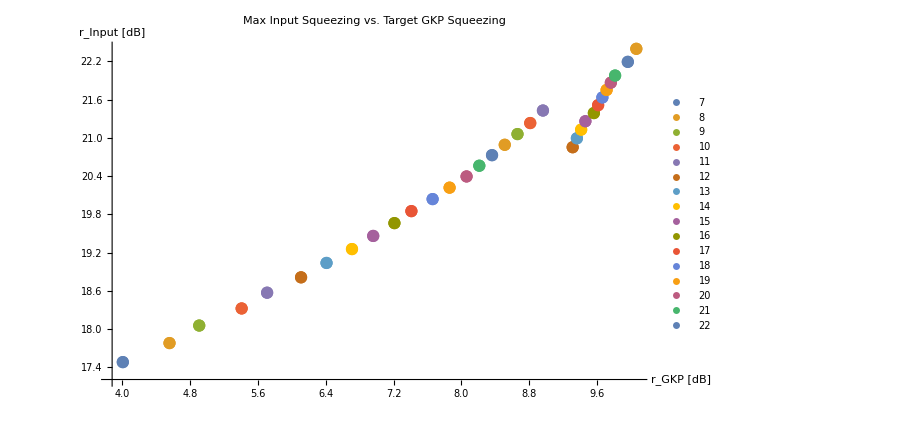

```mathematica
MaxSqueezing = Table[Max[PostDampingSqueezingValuesTable[[ii]]],{ii,1,Length[nSpace]}];
Get["Figure 2/TargetGKPSq"];
PlotMaxSq =Table[{{TargetGKPSq[[ii,2]],MaxSqueezing[[ii]]}},{ii,1,Length[nSpace]}];
P8 = ListPlot[PlotMaxSq,PlotLabel->"Max Input Squeezing vs. Target GKP Squeezing",AxesLabel->{Style["r_GKP [dB]",Large, Black],Style["r_Input [dB]",Large, Black]},TicksStyle->Directive[24],PlotLegends->Table[ToString[nSpace[[ii]]],{ii,1,Length[nSpace]}]];
Show[P8]
```